```mathematica
PhiHNew[x_,y_]:=(3-(I/8)*Sin[x/4]^2-Sin[x/4]^4 
-(I/8)*Sin[y/4]^8-Sin[y/4]^16
+(I/16)*(Sin[x]Cos[y]^2-2Sin[x]Cos[y] +Sin[x]) )/3
```

```mathematica
Series[PhiHNew[x,y],{x,0,4},{y,0,10}]
```

(1-(ⅈ y^8)/1572864+(ⅈ y^10)/18874368+O[y]^11)+((ⅈ y^4)/192-(ⅈ y^6)/1152+(ⅈ y^8)/15360-(17 ⅈ y^10)/5806080+O[y]^11) x-(ⅈ x^2)/384+(-(ⅈ y^4)/1152+(ⅈ y^6)/6912-(ⅈ y^8)/92160+(17 ⅈ y^10)/34836480+O[y]^11) x^3-(1/768-ⅈ/18432) x^4+O[x]^5

```mathematica
PhiHNew[0,0]
```

1

```mathematica
Series[Log[PhiHNew[x,y]/PhiHNew[0,0]],{x,0,2},{y,0,8}]
```

(-(ⅈ y^8)/1572864+O[y]^9)+((ⅈ y^4)/192-(ⅈ y^6)/1152+(ⅈ y^8)/15360+O[y]^9) x+(-ⅈ/384+(2731 y^8)/201326592+O[y]^9) x^2+O[x]^3

```mathematica
Show[Plot3D[1.000003Abs[PhiHNew[x,y]],{x,-2Pi,2Pi},{y,-2Pi,2Pi}],Plot3D[1,{x,-2Pi,2Pi},{y,-2Pi,2Pi}, PlotStyle-> {Black}]]
```

-Graphics3D-

```mathematica
RulePhiNew={Sin[x/2]->(1/(2I))(E^(I*x/2)-E^(-I*x/2)),
Sin[y/2]-> (1/(2I))(E^(I*y/2)-E^(-I*y/2)),
Sin[x]Sin[y/2]^2-> (1/(2I))(E^(I*x)-E^(-I*x))(1/(2I))(E^(I*y/2)-E^(-I*y/2))(1/(2I))(E^(I*y/2)-E^(-I*y/2)),
Sin[x/4]->(1/(2I))(E^(I*x/4)-E^(-I*x/4)),
Sin[x]->(1/(2I))(E^(I*x)-E^(-I*x)),
Cos[y]-> (1/(2))(E^(I*y)+E^(-I*y)),
Sin[y/4]-> (1/(2I))(E^(I*y/4)-E^(-I*y/4))};
```

```mathematica
PhiHNew[x,y]/.RulePhiNew//ExpandAll
```

(26527/32768-(33 ⅈ)/256)+(1/12+ⅈ/24) ⅇ^(-(ⅈ x)/2)+(1/12+ⅈ/24) ⅇ^((ⅈ x)/2)-ⅇ^(-ⅈ x)/192-(7 ⅇ^(ⅈ x))/192-1/96 ⅇ^(-ⅈ x-ⅈ y)+1/96 ⅇ^(ⅈ x-ⅈ y)-1/96 ⅇ^(-ⅈ x+ⅈ y)+1/96 ⅇ^(ⅈ x+ⅈ y)+1/384 ⅇ^(-ⅈ x-2 ⅈ y)-1/384 ⅇ^(ⅈ x-2 ⅈ y)+1/384 ⅇ^(-ⅈ x+2 ⅈ y)-1/384 ⅇ^(ⅈ x+2 ⅈ y)+(715/12288+(7 ⅈ)/192) ⅇ^(-(ⅈ y)/2)+(715/12288+(7 ⅈ)/192) ⅇ^((ⅈ y)/2)-(1001/24576+(7 ⅈ)/384) ⅇ^(-ⅈ y)-(1001/24576+(7 ⅈ)/384) ⅇ^(ⅈ y)+(91/4096+ⅈ/192) ⅇ^(-(3 ⅈ y)/2)+(91/4096+ⅈ/192) ⅇ^((3 ⅈ y)/2)-(455/49152+ⅈ/1536) ⅇ^(-2 ⅈ y)-(455/49152+ⅈ/1536) ⅇ^(2 ⅈ y)+(35 ⅇ^(-(5 ⅈ y)/2))/12288+(35 ⅇ^((5 ⅈ y)/2))/12288-(5 ⅇ^(-3 ⅈ y))/8192-(5 ⅇ^(3 ⅈ y))/8192+ⅇ^(-(7 ⅈ y)/2)/12288+ⅇ^((7 ⅈ y)/2)/12288-ⅇ^(-4 ⅈ y)/196608-ⅇ^(4 ⅈ y)/196608

```mathematica
HNew[i_,j_]:=NIntegrate[Cos[(-i*x/(100^(1/2))-j*y/(100^(1/8))-y^8/1536+y^4*x/192-x^2/24)],{x,-10,10},{y,-10,10}, PrecisionGoal -> 3,Method->"OscillatorySelection"]
data=Flatten[Table[{i,j,HNew[i,j]},{i,-7,7,0.1},{j,-7,7,0.1}],1];
Export["C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/dataNew6.csv",data,"CSV"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/dataNew1.csv

```mathematica
ListPlot3D[Import["C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/dataNew1.csv"],ColorFunction->Hue,PlotRange->Full]
```

-Graphics3D-

```mathematica
PhiHNew1[x_,y_]:=(3-(I)*Sin[x/4]^4-Sin[x/4]^8 
-(I)*Sin[y/3]^6-Sin[y/3]^12
+(I/64)*(Sin[x]^2Sin[y]^3 ) )/3
```

```mathematica
Series[PhiHNew1[x,y],{x,0,5},{y,0,9}]
```

(1-(ⅈ y^6)/2187+(ⅈ y^8)/19683+O[y]^10)+((ⅈ y^3)/192-(ⅈ y^5)/384+(13 ⅈ y^7)/23040-(41 ⅈ y^9)/580608+O[y]^10) x^2+(-ⅈ/768-(ⅈ y^3)/576+(ⅈ y^5)/1152-(13 ⅈ y^7)/69120+(41 ⅈ y^9)/1741824+O[y]^10) x^4+O[x]^6

```mathematica
PhiHNew1[0,0]
```

1

```mathematica
Series[Log[PhiHNew1[x,y]/PhiHNew1[0,0]],{x,0,4},{y,0,8}]
```

(-(ⅈ y^6)/2187+(ⅈ y^8)/19683+O[y]^9)+((ⅈ y^3)/192-(ⅈ y^5)/384+(13 ⅈ y^7)/23040+O[y]^9) x^2+(-ⅈ/768-(ⅈ y^3)/576+(ⅈ y^5)/1152+(761 y^6)/53747712-(13 ⅈ y^7)/69120-(6593 y^8)/483729408+O[y]^9) x^4+O[x]^5

```mathematica
Show[Plot3D[1.0001Abs[PhiHNew1[x,y]],{x,-3Pi,3Pi},{y,-3Pi,3Pi}],Plot3D[1,{x,-3Pi,3Pi},{y,-3Pi,3Pi}, PlotStyle-> {Black}]]
```

-Graphics3D-

```mathematica
RulePhiNew1={Sin[x/4]->(1/(2I))(E^(I*x/4)-E^(-I*x/4)),
Sin[y/6]-> (1/(2I))(E^(I*y/6)-E^(-I*y/6)),
Sin[x/2]->(1/(2I))(E^(I*x/2)-E^(-I*x/2)),
Sin[y/2]-> (1/(2I))(E^(I*y/2)-E^(-I*y/2)),
Sin[x]Sin[y/2]^2-> (1/(2I))(E^(I*x)-E^(-I*x))(1/(2I))(E^(I*y/2)-E^(-I*y/2))(1/(2I))(E^(I*y/2)-E^(-I*y/2)),
Sin[x]->(1/(2I))(E^(I*x)-E^(-I*x)),
Sin[y]->(1/(2I))(E^(I*y)+E^(-I*y))};
```

```mathematica
PhiHNew1[x,y]/.RulePhiNew1//ExpandAll
```

(349/384-ⅈ/8)+(7/96+ⅈ/12) ⅇ^(-(ⅈ x)/2)+(7/96+ⅈ/12) ⅇ^((ⅈ x)/2)-(7/192+ⅈ/48) ⅇ^(-ⅈ x)-(7/192+ⅈ/48) ⅇ^(ⅈ x)+1/96 ⅇ^(-(3 ⅈ x)/2)+1/96 ⅇ^((3 ⅈ x)/2)-1/768 ⅇ^(-2 ⅈ x)-1/768 ⅇ^(2 ⅈ x)+ⅇ^(-2 ⅈ x-ⅈ y)/2048+ⅇ^(2 ⅈ x-ⅈ y)/2048+ⅇ^(-2 ⅈ x+ⅈ y)/2048+ⅇ^(2 ⅈ x+ⅈ y)/2048+ⅇ^(-2 ⅈ x-3 ⅈ y)/6144+ⅇ^(2 ⅈ x-3 ⅈ y)/6144+ⅇ^(-2 ⅈ x+3 ⅈ y)/6144+ⅇ^(2 ⅈ x+3 ⅈ y)/6144-ⅇ^(-ⅈ y)/1024-ⅇ^(ⅈ y)/1024-ⅇ^(-3 ⅈ y)/3072-ⅇ^(3 ⅈ y)/3072-1/3 ⅈ Sin[y/3]^6-1/3 Sin[y/3]^12

```mathematica
HNew2[i_,j_]:=NIntegrate[Cos[(-i*x/(100000000^(1/4))-j*y/(100000000^(1/8))-y^8/768-y^4*x^2/192-x^4/48)],{x,-8,8},{y,-8,8}, PrecisionGoal -> 3,Method->"OscillatorySelection"]
data=Flatten[Table[{i,j,HNew2[i,j]},{i,-1000,1000,100},{j,-1000,1000,100}],1];
Export["C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/dataNew5.csv",data,"CSV"]
```

C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/dataNew5.csv

```mathematica
ListPlot3D[Import["C:/Users/buiqu/Documents/GitHub/huanium/Convolution Powers/dataNew5.csv"],ColorFunction->Hue,PlotRange->Full]
```

-Graphics3D-

```mathematica
MatrixExp[{{0,I*a},{I*a,0}}]
```

{{Cos[a],ⅈ Sin[a]},{ⅈ Sin[a],Cos[a]}}

```mathematica
MatrixExp[{{I*b,0},{0,-I*b}}]
```

{{ⅇ^(ⅈ b),0},{0,ⅇ^(-ⅈ b)}}

```mathematica
P[{{x_},{y_}}]:=x^2+y^4
```

```mathematica
EE={{1/2,0},{0,1/4}}
```

{{1/2,0},{0,1/4}}

```mathematica
MatrixExp[EE]
```

{{√ⅇ,0},{0,ⅇ^(1/4)}}

```mathematica
MatrixExp[EE].{{x},{y}}
```

{{√ⅇ x},{ⅇ^(1/4) y}}

```mathematica
P[MatrixExp[EE].{{x},{y}}]
```

ⅇ x^2+ⅇ y^4

```mathematica
OO={{1,0},{0,-1}}
```

{{1,0},{0,-1}}

```mathematica
P[OO.MatrixExp[EE].{{x},{y}}]
```

ⅇ x^2+ⅇ y^4

```mathematica
P[MatrixExp[EE].OO.{{x},{y}}]
```

ⅇ x^2+ⅇ y^4

```mathematica
MatrixExp[EE].OO-OO.MatrixExp[EE]
```

{{0,0},{0,0}}

```mathematica
MatrixExp[EE].OO
```

{{√ⅇ,0},{0,-ⅇ^(1/4)}}

```mathematica
Transpose[OO].MatrixExp[EE].OO
```

{{√ⅇ,0},{0,ⅇ^(1/4)}}

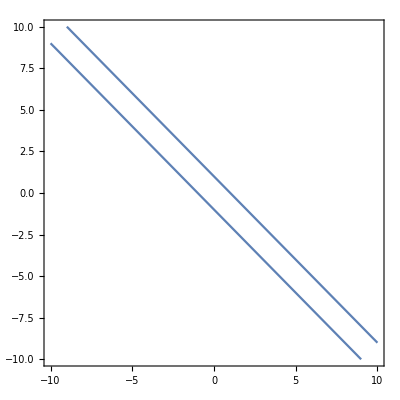

```mathematica
ContourPlot[x^2+y^2+2x*y==1,{x,-10,10},{y,-10,10}]
```

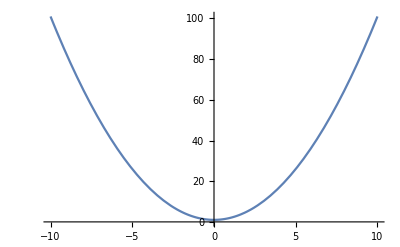

```mathematica
Plot[x^2+1,{x,-10,10}]
```

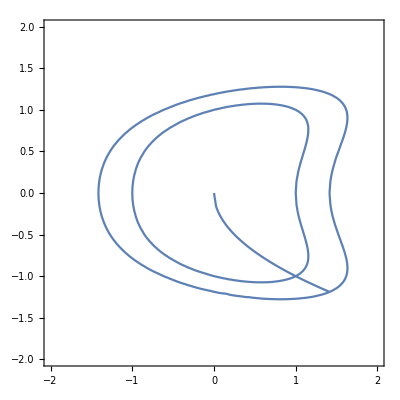

```mathematica
Show[ContourPlot[x^2+y^4-x*y^2==1,{x,-2,2},{y,-2,2}],
ContourPlot[x^2+y^4-x*y^2==2,{x,-2,2},{y,-2,2}],
ParametricPlot[{t^(1/2),-t^(1/4)},{t,0,2}]]
```

```mathematica
Norm[Grad[x^(1/4)+y^(1/4),{x,y}]]//Simplify
```

1/4 √(1/Abs[x]^(3/2)+1/Abs[y]^(3/2))

```mathematica
Plot3D[x^2+y^2-x*y,{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
MatrixExp[-({{1/2,0},{0,1/4}})]
```

{{1/(√ⅇ),0},{0,1/ⅇ^(1/4)}}

```mathematica
MatrixExp[{{1/4,0,0},{0,1/6,0},{0,0,1/8}}]
```

{{ⅇ^(1/4),0,0},{0,ⅇ^(1/6),0},{0,0,ⅇ^(1/8)}}

```mathematica
P[{{x_},{y_},{z_}}]:= x^4+y^4+z^4
```

```mathematica
{{1/4,0,0},{0,1/4,0},{0,0,1/4}}+{{0,1,2},{-3,0,3},{-2,-1,0}}//MatrixForm
```

(1/4 | 1 | 2
-3 | 1/4 | 3
-2 | -1 | 1/4)

```mathematica
MatrixExp[{{1/4,0,0},{0,1/4,0},{0,0,1/4}}+{{0,1,2},{-3,0,3},{-2,-1,0}}]//FullSimplify//MatrixForm
```

(1/10 ⅇ^(1/4) (3+7 Cos[√10]) | 1/10 ⅇ^(1/4) (-2+2 Cos[√10]+√10 Sin[√10]) | 1/10 ⅇ^(1/4) (3-3 Cos[√10]+2 √10 Sin[√10])
3/10 ⅇ^(1/4) (-2+2 Cos[√10]-√10 Sin[√10]) | 1/5 ⅇ^(1/4) (2+3 Cos[√10]) | 3/10 ⅇ^(1/4) (-2+2 Cos[√10]+√10 Sin[√10])
-1/10 ⅇ^(1/4) (-3+3 Cos[√10]+2 √10 Sin[√10]) | 1/10 ⅇ^(1/4) (-2+2 Cos[√10]-√10 Sin[√10]) | 1/10 ⅇ^(1/4) (3+7 Cos[√10]))

```mathematica
P[(MatrixExp[{{1/4,0,0},{0,1/4,0},{0,0,1/4}}+{{0,1,2},{-3,0,3},{-2,-1,0}}]).{{x},{y},{z}}]//FullSimplify
```

$Aborted

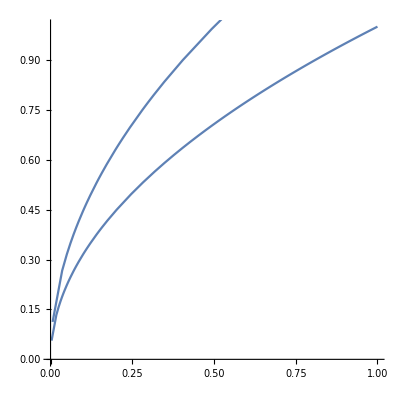

```mathematica
Show[ParametricPlot[{{t^(1/2),0},{0,t^(1/4)}}.{{1},{1}},{t,0.00001,1}],ParametricPlot[{{t^(1/2),0},{0,t^(1/4)}}.{{2},{2}},{t,0.00001,1}]]
```

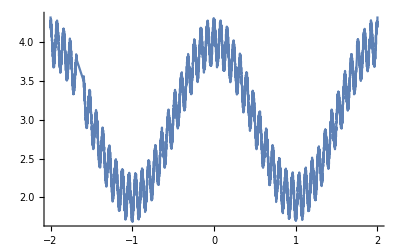

```mathematica
Plot[Sum[0.25^n*Cos[25^n*Pi*x],{n,0,100}]+3,{x,-2,2}]
```

```mathematica
WEI[x_]:= Sum[0.5^n*Cos[3^n*x],{n,0,50}]+3;
```

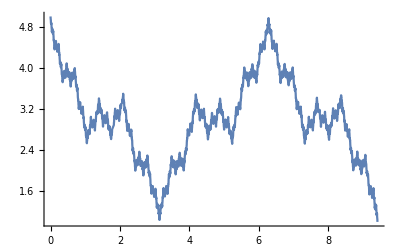

```mathematica
Plot[WEI[x],{x,0,3*Pi}]
```

```mathematica
P[x_,y_]:=Sqrt[x^2+y^2]*WEI[ArcTan[y/x]];
```

```mathematica
Plot3D[x^2+y^4,{x,-1.5,1.5},{y,-1.5,1.5}]
```

-Graphics3D-

```mathematica
Plot3D[P[x,y],{x,-1,1},{y,-1,1},ColorFunction->Function[{x,y,z},Hue[z]]]
```

-Graphics3D-

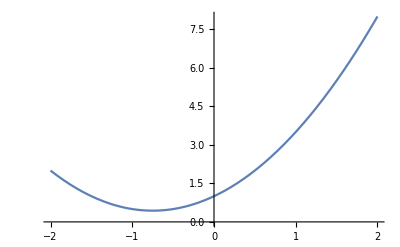

```mathematica
Plot[x^2+ 1.5*x+1,{x,-2,2}]
```

```mathematica
NIntegrate[Cos[t*(x^2+y^4-1)+(2*x+2^y)],{x,-10,10},{y,-10,10},{t,0,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.77174 and 0.0000348058 for the integral and error estimates.

4.77174

```mathematica
Plot3D[Cos[1*(x^2+y^4-1)+(2*x+2^y)],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
bb =(1-0.75^2)^(1/4)
```

0.813288

```mathematica
p1 = ParametricPlot[{Sqrt[1-a^4],a},{a,-0.75,0.75},PlotRange->{-1,1}];
```

```mathematica
p2 = ParametricPlot[{-Sqrt[1-a^4],-a},{a,-0.75,0.75},PlotRange->{-1,1}];
```

```mathematica
p3 = ParametricPlot[{b, -(1-b^2)^(1/4)},{b,-bb,bb},
PlotRange->{-1,1},PlotStyle->{Dashed,Red}];
```

```mathematica
p4 = ParametricPlot[{-b, (1-b^2)^(1/4)},{b,-bb,bb},
PlotRange->{-1,1},PlotStyle->{Dashed,Red}];
```

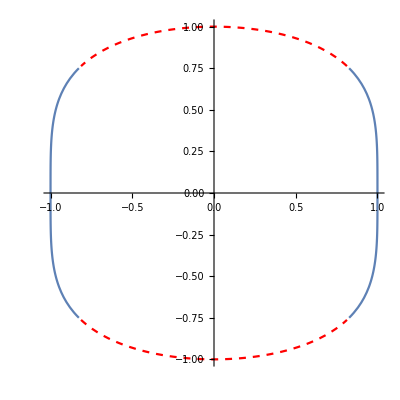

```mathematica
Show[p1,p2,p3,p4]
```

```mathematica
Phi[u_] := (1-u^4)^(1/2);
```

```mathematica
D[Phi[u],{u,4}]
```

-(240 u^12)/((1-u^4)^(7/2))-(432 u^8)/((1-u^4)^(5/2))-(204 u^4)/((1-u^4)^(3/2))-12/(√(1-u^4))

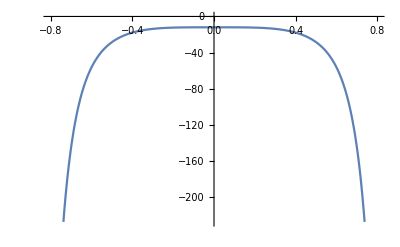

```mathematica
Plot[-(240 u^12)/((1-u^4)^(7/2))-(432 u^8)/((1-u^4)^(5/2))-(204 u^4)/((1-u^4)^(3/2))-12/(√(1-u^4)),{u,-0.8,0.8}]
```

```mathematica
PhiA[u_]:=ξ1*Sqrt[1-u^4]+ ξ2*u
```

```mathematica
D[ξ1*Sqrt[1-u^4]+ ξ2*u,u]
```

-(2 u^3 ξ1)/(√(1-u^4))+ξ2

```mathematica
Manipulate[Show[Plot[ξ1*Sqrt[1-u^4]+ ξ2*u,{u,-1,1},PlotRange->All],
 Plot[-(2 u^3 ξ1)/(√(1-u^4))+ξ2,{u,-1,1},PlotStyle->{Dashed,Red}],
Plot[(-(4 u^6)/((1-u^4)^(3/2))-(6 u^2)/(√(1-u^4))) ξ1,{u,-1,1},PlotStyle->{Dashed,Black}]],{ξ1,-10,10},{ξ2,-10,10}]
```

```mathematica
D[PhiA[u],{u,1}]
```

-(2 u^3 ξ1)/(√(1-u^4))+ξ2

```mathematica
PhiA2[u_]:=(-(4 u^6)/((1-u^4)^(3/2))-(6 u^2)/(√(1-u^4))) *t;
```

```mathematica
PhiA2[r^(1/3)]//Expand
```

-(4 r^2 t)/((1-r^(4/3))^(3/2))-(6 r^(2/3) t)/(√(1-r^(4/3)))

```mathematica
Series[1/Sqrt[-PhiA2[r^(1/3)]],{r,0,3},{t,Infinity,3}]//Simplify
```

((√(1/t))/(√6)+O[1/t]^(7/2))/r^(1/3)+(-(7 √(1/t))/(12 √6)+O[1/t]^(7/2)) r+(-(17 √(1/t))/(96 √6)+O[1/t]^(7/2)) r^(7/3)+O[r]^(10/3)

```mathematica
Series[(√(-r^2+r^4/((216 r^2-r^6+12 √3 √(-r^4 (-108+r^4)))^(1/3))+(216 r^2-r^6+12 √3 √(-r^4 (-108+r^4)))^(1/3)))/(2 √3),{r,0,5}]
```

r^(1/3)/2^(1/3)-r^(5/3)/(12 2^(2/3))+r^3/192-(7 r^(13/3))/(20736 2^(1/3))+O[r]^(16/3)

```mathematica
1/4+1/6
```

5/12

```mathematica
Integrate[E^(-I*t)*t^(-5/12),{t,-Infinity,Infinity}]
```

-(-1)^(17/24) (1+(-1)^(1/6)) Gamma[7/12]

```mathematica
216 ξ1^4 ξ2^2-ξ2^6+12 √(324 ξ1^8 ξ2^4-3 ξ1^4 ξ2^8)
```

```mathematica
ξ2^2(216 ξ1^4 -ξ2^4+12 ξ1^2  √(324 ξ1^4 -3 ξ2^4))
```

ξ2^2 (216 ξ1^4-ξ2^4+12 ξ1^2 √(324 ξ1^4-3 ξ2^4))

```mathematica
Solve[-(2 u^3 *ξ1)/(√(1-u^4))+ξ2==0,u]
```

{{u→-(√(-ξ2^2/ξ1^2+ξ2^4/(ξ1^2 (216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(ξ1^4 ξ2^4 (108 ξ1^4-ξ2^4)))^(1/3))+((216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(ξ1^4 ξ2^4 (108 ξ1^4-ξ2^4)))^(1/3))/ξ1^2))/(2 √3)},{u→(√(-ξ2^2/ξ1^2+ξ2^4/(ξ1^2 (216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(ξ1^4 ξ2^4 (108 ξ1^4-ξ2^4)))^(1/3))+((216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(ξ1^4 ξ2^4 (108 ξ1^4-ξ2^4)))^(1/3))/ξ1^2))/(2 √3)},{u→-√(-ξ2^2/(12 ξ1^2)-ξ2^4/(24 ξ1^2 (216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))+(ⅈ ξ2^4)/(8 √3 ξ1^2 (216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))-((216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))/(24 ξ1^2)-(ⅈ (216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))/(8 √3 ξ1^2))},{u→√(-ξ2^2/(12 ξ1^2)-ξ2^4/(24 ξ1^2 (216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))+(ⅈ ξ2^4)/(8 √3 ξ1^2 (216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))-((216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))/(24 ξ1^2)-(ⅈ (216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))/(8 √3 ξ1^2))},{u→-√(-ξ2^2/(12 ξ1^2)-ξ2^4/(24 ξ1^2 (216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))-(ⅈ ξ2^4)/(8 √3 ξ1^2 (216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))-((216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))/(24 ξ1^2)+(ⅈ (216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))/(8 √3 ξ1^2))},{u→√(-ξ2^2/(12 ξ1^2)-ξ2^4/(24 ξ1^2 (216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))-(ⅈ ξ2^4)/(8 √3 ξ1^2 (216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))-((216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))/(24 ξ1^2)+(ⅈ (216 ξ1^4 ξ2^2-ξ2^6+12 √3 √(108 ξ1^8 ξ2^4-ξ1^4 ξ2^8))^(1/3))/(8 √3 ξ1^2))}}

```mathematica
Manipulate[Plot[(-(4 u^6)/((1-u^4)^(3/2))-(6 u^2)/(√(1-u^4))) ξ1,{u,-1,1}],{ξ1,-10,10},{ξ2,-10,10}]
```

```mathematica
Manipulate[Plot[(-(240 u^12)/((1-u^4)^(7/2))-(432 u^8)/((1-u^4)^(5/2))-(204 u^4)/((1-u^4)^(3/2))-12/(√(1-u^4))) ξ1,{u,-0.75,0.75}],{ξ1,-10,10},{ξ2,-10,10}]
```

```mathematica
P[x_,y_] := x^2+y^4;
```

```mathematica
Plot3D[1/P[x,y]^(1/8),{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
D[1/a + (1/x1)*((a-x2)^(1/3) + (a+x2)^(1/3)),a]//Simplify
```

-1/a^2+(1/(a-x2)^(2/3)+1/(a+x2)^(2/3))/(3 x1)

```mathematica
Solve[-1/a^2+(1/(a-x2)^(2/3)+1/(a+x2)^(2/3))/(3 x1)==0,a]
```

$Aborted

```mathematica
Solve[u^3+ x*u^2-x==0,u]
```

{{u→1/3 (-x+(2^(1/3) x^2)/((27 x-2 x^3+3 √3 √(27 x^2-4 x^4))^(1/3))+((27 x-2 x^3+3 √3 √(27 x^2-4 x^4))^(1/3))/2^(1/3))},{u→-x/3-((1+ⅈ √3) x^2)/(3 2^(2/3) (27 x-2 x^3+3 √3 √(27 x^2-4 x^4))^(1/3))-((1-ⅈ √3) (27 x-2 x^3+3 √3 √(27 x^2-4 x^4))^(1/3))/(6 2^(1/3))},{u→-x/3-((1-ⅈ √3) x^2)/(3 2^(2/3) (27 x-2 x^3+3 √3 √(27 x^2-4 x^4))^(1/3))-((1+ⅈ √3) (27 x-2 x^3+3 √3 √(27 x^2-4 x^4))^(1/3))/(6 2^(1/3))}}

```mathematica
Sqrt[1/3 (-x+(2^(1/3) x^2)/((27 x-2 x^3+3 √3 √(27 x^2-4 x^4))^(1/3))+((27 x-2 x^3+3 √3 √(27 x^2-4 x^4))^(1/3))/2^(1/3))]//Simplify
```

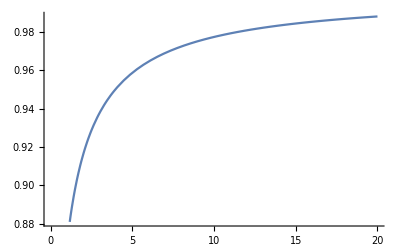

```mathematica
Plot[(√(-x+(2^(1/3) x^2)/((27 x-2 x^3+3 √(81 x^2-12 x^4))^(1/3))+((27 x-2 x^3+3 √(81 x^2-12 x^4))^(1/3))/2^(1/3)))/(√3),{x,0,20}]
```

```mathematica
f[x_]:=(√(-x+(2^(1/3) x^2)/((27 x-2 x^3+3 √(81 x^2-12 x^4))^(1/3))+((27 x-2 x^3+3 √(81 x^2-12 x^4))^(1/3))/2^(1/3)))/(√3);
```

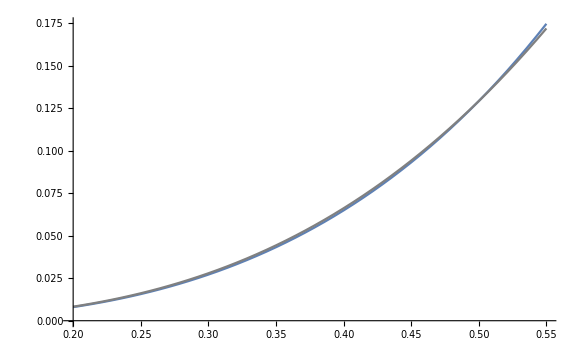

```mathematica
Show[Plot[u^3/Sqrt[(1-u^4)],{u,0.2,0.55}],Plot[(1/(Sqrt[1-0.5^4]))*u^3,{u,0.2,0.55},PlotStyle->Gray]]
```

```mathematica
Series[u^3/Sqrt[(1-u^4)],{u,0,6}]
```

u^3+O[u]^7

```mathematica
(x2-(2*u^3*x1)/Sqrt[1-u^4])^2//Expand//TeXForm
```

\frac{4 u^6 \text{x1}^2}{1-u^4}-\frac{4 u^3 \text{x1}
   \text{x2}}{\sqrt{1-u^4}}+\text{x2}^2

```mathematica
(f[(ξ2+α)^2/(4*ξ1^2)]-f[(ξ2-α)^2/(4*ξ1^2)])*2//FullSimplify
```

1/(√3)(-√(((216 (α-ξ2)^2)/ξ1^2-(α-ξ2)^6/ξ1^6+12 √3 √(-((-108 ξ1^4+(α-ξ2)^4) (α-ξ2)^4)/ξ1^8))^(1/3)-(α-ξ2)^2/ξ1^2+(α-ξ2)^4/(ξ1^4 ((216 (α-ξ2)^2)/ξ1^2-(α-ξ2)^6/ξ1^6+12 √3 √(-((-108 ξ1^4+(α-ξ2)^4) (α-ξ2)^4)/ξ1^8))^(1/3)))+√(-(α+ξ2)^2/ξ1^2+(α+ξ2)^4/(ξ1^4 ((216 (α+ξ2)^2)/ξ1^2-(α+ξ2)^6/ξ1^6+12 √3 √(-((α+ξ2)^4 (-108 ξ1^4+(α+ξ2)^4))/ξ1^8))^(1/3))+((216 (α+ξ2)^2)/ξ1^2-(α+ξ2)^6/ξ1^6+12 √3 √(-((α+ξ2)^4 (-108 ξ1^4+(α+ξ2)^4))/ξ1^8))^(1/3)))

```mathematica
((α+ξ2)/(2ξ1))^(1/3)
```

((α+ξ2)/ξ1)^(1/3)/2^(1/3)

```mathematica
f[u_] := x1*Sqrt[1-u^4]+x2*u;
```

```mathematica
D[f[u],u]//TeXForm
```

\text{x2}-\frac{2 u^3 \text{x1}}{\sqrt{1-u^4}}

```mathematica
D[(1/α)+((ξ2+α)/(2*ξ1))^(1/3)-((ξ2-α)/(2*ξ1))^(1/3),{α,1}]
```

-1/α^2+1/(3 2^(1/3) ξ1 ((-α+ξ2)/ξ1)^(2/3))+1/(3 2^(1/3) ξ1 ((α+ξ2)/ξ1)^(2/3))

```mathematica
Solve[a^6 - (x+a)*x*C==0,a]
```

{{a→Root[-C x^2-C x #1+#1^6&,1]},{a→Root[-C x^2-C x #1+#1^6&,2]},{a→Root[-C x^2-C x #1+#1^6&,3]},{a→Root[-C x^2-C x #1+#1^6&,4]},{a→Root[-C x^2-C x #1+#1^6&,5]},{a→Root[-C x^2-C x #1+#1^6&,6]}}

```mathematica
N@Root[-4-4 #1+#1^6&,1]
```

-0.88217

```mathematica
Ca = 0.5^3/Sqrt[1-0.5^4];
```

```mathematica
D[(1/α)+((ξ2+α)/(2*1*ξ1))^(1/3) - ((ξ2-α)/(2*Ca*ξ1))^(1/3),{α,1}]
```

-1/α^2+0.523473/(ξ1 ((-α+ξ2)/ξ1)^(2/3))+1/(3 2^(1/3) ξ1 ((α+ξ2)/ξ1)^(2/3))

```mathematica
Manipulate[Show[Plot[(1/α)+((ξ2+α)/(2*1*ξ1))^(1/3) - ((ξ2-α)/(2*Ca*ξ1))^(1/3),{α,0,100}],Plot[-1/α^2+0.5234726008250066/(ξ1 ((-α+ξ2)/ξ1)^(2/3))+1/(3 2^(1/3) ξ1 ((α+ξ2)/ξ1)^(2/3)),{α,0,100}]],{ξ1,10,1000},{ξ2,1,200}]
```

```mathematica
Manipulate[Plot[(1/α)+((ξ2+α)/(2*1*ξ1))^(1/3),{α,10,200}] ,{ξ1,10,1000},{ξ2,1,10}]
```

```mathematica
Manipulate[Plot[1/α + α^(1/(k-1)),{α,0.01,100}],{k,0.01,5}]
```

```mathematica
-√(((216 (α-ξ2)^2)/ξ1^2-(α-ξ2)^6/ξ1^6+12 √3 √(-((-108 ξ1^4+(α-ξ2)^4) (α-ξ2)^4)/ξ1^8))^(1/3))+√(((216 (α+ξ2)^2)/ξ1^2-(α+ξ2)^6/ξ1^6+12 √3 √(-((α+ξ2)^4 (-108 ξ1^4+(α+ξ2)^4))/ξ1^8))^(1/3))
```

```mathematica
-((216 (α-ξ2)^2)/ξ1^2+12 √3 √(-((-108 ξ1^4+(α-ξ2)^4) (α-ξ2)^4)/ξ1^8))^(1/6)+((216 (α+ξ2)^2)/ξ1^2+12 √3 √(-((α+ξ2)^4 (-108 ξ1^4+(α+ξ2)^4))/ξ1^8))^(1/6)
```

```mathematica
-((216 (α-ξ2)^2)/ξ1^2)^(1/6)+((216 (α+ξ2)^2)/ξ1^2)^(1/6)
```

-√6 ((α-ξ2)^2/ξ1^2)^(1/6)+√6 ((α+ξ2)^2/ξ1^2)^(1/6)

```mathematica
ff[α_]:=(1/α)- ((α-ξ2)^2/ξ1^2)^(1/6)+ ((α+ξ2)^2/ξ1^2)^(1/6);
```

```mathematica
D[ff[α],{α,1}]//Simplify
```

1/3 (-3/α^2-(((α-ξ2)^2/ξ1^2)^(1/6))/(α-ξ2)+(((α+ξ2)^2/ξ1^2)^(1/6))/(α+ξ2))

```mathematica
Solve[-3/α^2-(((α-ξ2)^2/ξ1^2)^(1/6))/(α-ξ2)+(((α+ξ2)^2/ξ1^2)^(1/6))/(α+ξ2)==0,α]
```

$Aborted

```mathematica
Phi[u_]:=ξ1*Sqrt[1-u^4]+ξ2*u;
```

```mathematica
D[Phi[u],u]
```

-(2 u^3 ξ1)/(√(1-u^4))+ξ2

```mathematica
Manipulate[Plot[Piecewise[{{((ξ2+α)/(2*ξ1))^(1/3),α≤ξ2},
{((ξ2+α)/(2*ξ1))^(1/3)+Abs[(ξ2-α)/(2*ξ1)]^(1/3),-α≤ξ2<α}}],{α,0.01,50}],{ξ2,-20,20},{ξ1,0.01,100000}]
```

```mathematica
Manipulate[Plot[Piecewise[{{1/α+((ξ2+α)/(2*ξ1))^(1/3),α≤ξ2},
{1/α+((ξ2+α)/(2*ξ1))^(1/3)+Abs[(ξ2-α)/(2*ξ1)]^(1/3),-α≤ξ2<α}}],{α,0.01,50}],{ξ2,-20,20},{ξ1,0.01,100000}]
```

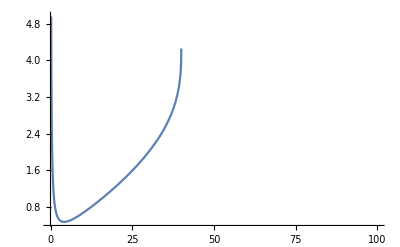

```mathematica
Plot[1/α+(40+α)^(1/3)-(40-α)^(1/3),{α,0.01,100}]
```

```mathematica
N[1/60+(40+60)^(1/3)-(40-60)^(1/3)]
```

3.30105-2.35075 ⅈ

```mathematica
N[(40-60)^(1/3)]
```

1.35721+2.35075 ⅈ

```mathematica
N[(-1)^(1/3)]
```

0.5+0.866025 ⅈ

```mathematica
Manipulate[Show[Plot[1/(δ+1)^(2/3)+1/(δ-1)^(2/3),{δ,1.1,10},PlotRange->Full,ColorFunction->Hue],Plot[(1/δ^2)*(ξ2)^(-4/3),{δ,1.1,10},PlotRange->Full]],{ξ2,0.01,100}]
```

```mathematica
Manipulate[Plot[-1/α^2+1/(3 2^(1/3) ξ1 ((α(-1+δ))/ξ1)^(2/3))+1/(3 2^(1/3) ξ1 ((α(1+δ))/ξ1)^(2/3)),{α,0.01,10}],{δ,0.01,0.99},{ξ1,0.01,100}]
```

```mathematica
D[1/α+((ξ2+α)/(2*ξ1))^(1/3)-((ξ2-α)/(2*ξ1))^(1/3),{α,1}]
```

-1/α^2+1/(3 2^(1/3) ξ1 ((-α+ξ2)/ξ1)^(2/3))+1/(3 2^(1/3) ξ1 ((α+ξ2)/ξ1)^(2/3))

```mathematica
(ξ1^(1/4) + ξ2^(1/2))
```

```mathematica
-1/(((ξ1^(1/4) + ξ2^(1/2)))^2)+1/(3 2^(1/3) ξ1 ((-((ξ1^(1/4) + ξ2^(1/2)))+ξ2)/ξ1)^(2/3))+1/(3 2^(1/3) ξ1 (((ξ1^(1/4) + ξ2^(1/2))+ξ2)/ξ1)^(2/3))//Simplify
```

1/6 (-6/((ξ1^(1/4)+√ξ2)^2)+2^(2/3)/(ξ1 (-(ξ1^(1/4)+√ξ2-ξ2)/ξ1)^(2/3))+2^(2/3)/(ξ1 ((ξ1^(1/4)+√ξ2+ξ2)/ξ1)^(2/3)))

```mathematica
1/(ξ1^(1/4) + ξ2^(1/2))+((ξ2+(ξ1^(1/4) + ξ2^(1/2)))/(2*ξ1))^(1/3)+((ξ2-(ξ1^(1/4) + ξ2^(1/2)))/(2*ξ1))^(1/3)//Simplify
```

1/(ξ1^(1/4)+√ξ2)+((-(ξ1^(1/4)+√ξ2-ξ2)/ξ1)^(1/3))/2^(1/3)+(((ξ1^(1/4)+√ξ2+ξ2)/ξ1)^(1/3))/2^(1/3)

```mathematica
D[ξ1*Sqrt[1-u^4]+ξ2*u,u]
```

-(2 u^3 ξ1)/(√(1-u^4))+ξ2

```mathematica
D[ξ1*u-ξ2*(1-u^2)^(1/4),u]
```

ξ1+(u ξ2)/(2 (1-u^2)^(3/4))

```mathematica
N[(1-0.75^2)^(1/4)]
```

0.813288

```mathematica
Manipulate[Show[Plot[-(2 u^3 ξ1)/(√(1-u^4))+ξ2,{u,-0.75,0.75},ColorFunction->Hue],Plot[ξ1+(u ξ2)/(2 (1-u^2)^(3/4)),{u,-(1-0.75^2)^(1/4),(1-0.75^2)^(1/4)},ColorFunction->GrayLevel],Plot[0,{u,-1,1}]],{ξ1,0,20},{ξ2,-20,20}]
```

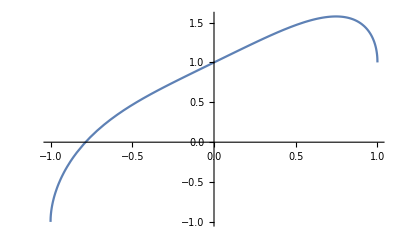

```mathematica
Plot[Sqrt[1-u^4]+u,{u,-1,1}]
```

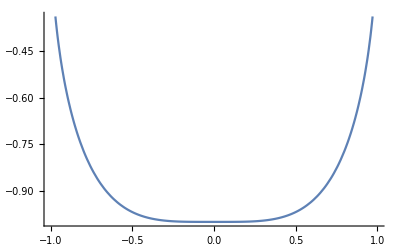

```mathematica
Plot[-Sqrt[1-u^4],{u,-1,1}]
```

```mathematica
Series[ξ1*Sqrt[1-u^4]+ξ2*u,{u,u0,5}]//Simplify
```

(√(1-u0^4) ξ1+u0 ξ2)+(-(2 u0^3 ξ1)/(√(1-u0^4))+ξ2) (u-u0)+(u0^2 (-3+u0^4) ξ1 (u-u0)^2)/((1-u0^4)^(3/2))-(2 (u0 (1+u0^4) ξ1) (u-u0)^3)/((1-u0^4)^(5/2))-(((1+14 u0^4+5 u0^8) ξ1) (u-u0)^4)/(2 (1-u0^4)^(7/2))-(u0^3 (7+18 u0^4+3 u0^8) ξ1 (u-u0)^5)/((1-u0^4)^(9/2))+O[u-u0]^6

```mathematica
Series[Exp[-I*(ξ1*Sqrt[1-u^4] + ξ2*u)],{u,0,7}]/E^(-I*ξ1)
```

1-ⅈ ξ2 u-(ξ2^2 u^2)/2+1/6 ⅈ ξ2^3 u^3+1/24 (12 ⅈ ξ1+ξ2^4) u^4+1/120 ξ2 (60 ξ1-ⅈ ξ2^4) u^5-1/720 (ξ2^2 (180 ⅈ ξ1+ξ2^4)) u^6-((ξ2^3 (420 ξ1-ⅈ ξ2^4)) u^7)/5040+O[u]^8

```mathematica
Integrate[(u^2/Sqrt[1-u^4]),{u,-0.75,0.75}]
```

0.303915-3.13188×10^-17 ⅈ

```mathematica
1/D[(1-u^4)^(1/2)+(δ)*u,{u,1}]
```

1/(-(2 u^3)/(√(1-u^4))+δ)

```mathematica
1/(-(2 u^3)/(√(1-u^4))+δ)-1/((2 u^3)/(√(1-u^4))+δ)//FullSimplify
```

-(4 u^3 √(1-u^4))/(4 u^6+(-1+u^4) δ^2)

```mathematica
1/(4*a^6*ξ1^2-(1-a^4)*ξ2^2)+(1-a^2)^(1/4)*ξ1^2/(4*(1-(1-a^2)^(1/2))^(3/2)*ξ1^2-((1-a^2)^(1/2))*ξ2^2)//FullSimplify
```

((1-a^2)^(1/4) ξ1^2)/(4 (1-√(1-a^2))^(3/2) ξ1^2-√(1-a^2) ξ2^2)+1/(4 a^6 ξ1^2+(-1+a^4) ξ2^2)

```mathematica
(4*a^6*ξ1^2-(1-a^4)*ξ2^2)*(4*(1-(1-a^2)^(1/2))^(3/2)*ξ1^2-((1-a^2)^(1/2))*ξ2^2)//Simplify
```

(4 a^6 ξ1^2-ξ2^2+a^4 ξ2^2) (4 (1-√(1-a^2))^(3/2) ξ1^2-√(1-a^2) ξ2^2)

```mathematica
D[(1-u^2)^(1/4)-(1/δ)*u,{u,1}]
```

-u/(2 (1-u^2)^(3/4))-1/δ

```mathematica
(-u/(2 (1-u^2)^(3/4))-1/δ)^(-1)-(u/(2 (1-u^2)^(3/4))-1/δ)^(-1)//FullSimplify
```

(4 u (1-u^2)^(3/4) δ^2)/((2 (1-u^2)^(3/4)-u δ) (2 (1-u^2)^(3/4)+u δ))

```mathematica
1/(-(2 u^3)/(√(1-u^4))+δ)-1/((2 u^3)/(√(1-u^4))+δ)//FullSimplify
```

-(4 u^3 √(1-u^4))/(4 u^6+(-1+u^4) δ^2)

```mathematica
Manipulate[Plot[-(3 u^2)/(4 (1-u^2)^(7/4))-1/(2 (1-u^2)^(3/4)),{u,-0.99,0.99}],{δ,-100,100}]
```

```mathematica
Manipulate[Plot[Sqrt[1-u^4]+δ*u,{u,-0.75,0.75}],{δ,-100,100}]
```

```mathematica
Plot3D[1/(Abs[4*0.75^6*ξ1^2 - (1-0.75^4)*ξ2^2]),{ξ1,-10,10},{ξ2,0,100}]
```

-Graphics3D-

```mathematica
NSolve[4*a^6+(1-a^4)==0,a]
```

{{a→-0.732626-0.365232 ⅈ},{a→-0.732626+0.365232 ⅈ},{a→0.-0.746119 ⅈ},{a→0.+0.746119 ⅈ},{a→0.732626-0.365232 ⅈ},{a→0.732626+0.365232 ⅈ}}

```mathematica
Manipulate[Show[Plot3D[1/(Abs[4*a^6*ξ1^2-(1-a^4)ξ2^2]),{ξ1,-5,5},{ξ2,-5,5}]],{a,-1,1}]
```

```mathematica
Manipulate[Plot[Abs[4*a^6*ξ1^2-(1-a^4)ξ2^2],{a,-1,1}],{ξ1,-5,5},{ξ2,-5,5}]]
```

```mathematica
D[4*a^6*ξ1^2-(1-a^4)ξ2^2,a]
```

24 a^5 ξ1^2+4 a^3 ξ2^2

```mathematica
D[E^(I*ξ2*u)/Sqrt[1-u^4],{u,1}]
```

(2 ⅇ^(ⅈ u ξ2) u^3)/((1-u^4)^(3/2))+(ⅈ ⅇ^(ⅈ u ξ2) ξ2)/(√(1-u^4))

```mathematica
Phi[u_]:= x1*Sqrt[1-u^4]+x2*u;
```

```mathematica
w[u_]:=1/Sqrt[1-u^4];
```

```mathematica
w[u]/D[Phi[u],u]
```

1/(√(1-u^4) (-(2 u^3 x1)/(√(1-u^4))+x2))

```mathematica
Manipulate[Plot[1/(√(1-u^4) (-(2 u^3 x1)/(√(1-u^4))+x2)),{u,-1,1}],{x1,-10,10},{x2,-10,10}]
```

```mathematica
D[E^(I*ξ2*u)/(2*Sqrt[1-u^4]),u]
```

(ⅇ^(ⅈ u ξ2) u^3)/((1-u^4)^(3/2))+(ⅈ ⅇ^(ⅈ u ξ2) ξ2)/(2 √(1-u^4))

```mathematica
D[Sqrt[1-u^4],u]
```

-(2 u^3)/(√(1-u^4))

```mathematica
Integrate[1/(2*Sqrt[1-u^4]),{u,-a,a}]
```

ConditionalExpression[a Hypergeometric2F1[1/4,1/2,5/4,a^4],0<Re[a]<1&&Im[a]==0]

```mathematica
Integrate[Abs[u^3]/(1-u^4)^(3/2),{u,-a,a}]
```

ConditionalExpression[-1+1/(√(1-a^4)),0<Re[a]<1&&Im[a]==0]

```mathematica
D[Sqrt[1-u^4],{u,4}]
```

-(240 u^12)/((1-u^4)^(7/2))-(432 u^8)/((1-u^4)^(5/2))-(204 u^4)/((1-u^4)^(3/2))-12/(√(1-u^4))

```mathematica
FindMaximum[-(240 u^12)/((1-u^4)^(7/2))-(432 u^8)/((1-u^4)^(5/2))-(204 u^4)/((1-u^4)^(3/2))-12/(√(1-u^4)),{u,-0.99,0.99}]
```

{-12.,{u→-0.00252026}}

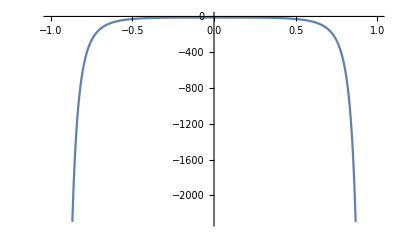

```mathematica
Plot[-(240 u^12)/((1-u^4)^(7/2))-(432 u^8)/((1-u^4)^(5/2))-(204 u^4)/((1-u^4)^(3/2))-12/(√(1-u^4)),{u,-1,1}]
```

```mathematica
psi[u_]:=E^(I*ξ2*u)/(2*Sqrt[1-u^4]);
```

```mathematica
D[psi[u],u]//TeXForm
```

\frac{i \text{$\xi $2} e^{i \text{$\xi $2} u}}{2 \sqrt{1-u^4}}+\frac{u^3 e^{i
   \text{$\xi $2} u}}{\left(1-u^4\right)^{3/2}}

```mathematica
D[Sqrt[1-u^4],u]
```

-(2 u^3)/(√(1-u^4))

```mathematica
ratio[u_]:=psi[u]/(-(2 u^3)/(√(1-u^4)))
```

```mathematica
D[ratio[u],u]
```

(3 ⅇ^(ⅈ u ξ2))/(4 u^4)-(ⅈ ⅇ^(ⅈ u ξ2) ξ2)/(4 u^3)

```mathematica
Integrate[Abs[(3/u^4-1/u^3)*(E^(-I*u))],{u,-a,a}]
```

Integrate::idiv: Integral of ⅇ^Im[u]\ Abs[3 - u/u^4] does not converge on {-a, a}.

∫_-a^a ⅇ^Im[u] Abs[3/u^4-1/u^3]ⅆu

```mathematica
ratio[u_]:=(E^(I*ξ2*u)/(2*Sqrt[1-u^4]))/-(2 u^3)/(√(1-u^4))
```

```mathematica
ratio[u]
```

-ⅇ^(ⅈ u ξ2)/(4 u^3)

```mathematica
ratio[a]-ratio[-a]
```

-ⅇ^(-ⅈ a ξ2)/(4 a^3)-ⅇ^(ⅈ a ξ2)/(4 a^3)

```mathematica
D[(1/2)*E^(-I*ξ1*Sqrt[1-u^4])/Sqrt[1-u^4],u]
```

(ⅇ^(-ⅈ √(1-u^4) ξ1) u^3)/((1-u^4)^(3/2))+(ⅈ ⅇ^(-ⅈ √(1-u^4) ξ1) u^3 ξ1)/(1-u^4)

```mathematica
Integrate[Abs[ u^3]/((1-u^4)^(3/2)),{u,-a,a}]
```

ConditionalExpression[-1+1/(√(1-a^4)),0<Re[a]<1&&Im[a]==0]

```mathematica
Integrate[(2  Abs[u^3] ξ1)/(1-u^4),{u,-a,a}]
```

ConditionalExpression[-ξ1 Log[1-a^4],0<Re[a]<1&&Im[a]==0]

```mathematica
Integrate[(2 u^3)/((1-u^4)^(3/2)),{u,-a,a}]
```

0

```mathematica
Integrate[ξ2/(√(1-u^4)),{u,-a,a}]
```

ConditionalExpression[2 a ξ2 Hypergeometric2F1[1/4,1/2,5/4,a^4],0<Re[a]<1&&Im[a]==0]

```mathematica
D[E^(-I*ξ1*u)/(1-u^2)^(1/4),u]
```

(ⅇ^(-ⅈ u ξ1) u)/(2 (1-u^2)^(5/4))-(ⅈ ⅇ^(-ⅈ u ξ1) ξ1)/((1-u^2)^(1/4))

```mathematica
psi[u_]:=E^(I*ξ2(1-u^2)^(1/4))/(4*(1-u^2)^(3/4))
```

```mathematica
phi[u_]:=u
```

```mathematica
D[psi[u],u]
```

(3 ⅇ^(ⅈ (1-u^2)^(1/4) ξ2) u)/(8 (1-u^2)^(7/4))-(ⅈ ⅇ^(ⅈ (1-u^2)^(1/4) ξ2) u ξ2)/(8 (1-u^2)^(3/2))

```mathematica
Integrate[(3 Abs[u])/(8 (1-u^2)^(7/4)),{u,-a,a}]
```

ConditionalExpression[1/2 (-1+1/((1-a^2)^(3/4))),0<Re[a]<1&&Im[a]==0]

```mathematica
Integrate[(Abs[u] ξ2)/(8 (1-u^2)^(3/2)),{u,-a,a}]
```

ConditionalExpression[1/4 (-1+1/(√(1-a^2))) ξ2,0<Re[a]<1&&Im[a]==0]

```mathematica
psi[u_]:=E^(I*ξ1*u)/(4*(1-u^2)^(3/4))
```

```mathematica
phi[u_]:=(1-u^2)^(1/4)
```

```mathematica
D[phi[u],u]
```

-u/(2 (1-u^2)^(3/4))

```mathematica
ratio[u_]:=psi[u]/-u/(2 (1-u^2)^(3/4))
```

```mathematica
ratio[b] - ratio[-b]
```

-ⅇ^(-ⅈ b ξ1)/(2 b)-ⅇ^(ⅈ b ξ1)/(2 b)

```mathematica
D[psi[u]/-u/(2 (1-u^2)^(3/4)),u]
```

ⅇ^(ⅈ u ξ1)/(2 u^2)-(ⅈ ⅇ^(ⅈ u ξ1) ξ1)/(2 u)

```mathematica
Integrate[Abs[u^3]/(1-u^4)^(3/2),{u,-a,a}]
```

ConditionalExpression[-1+1/(√(1-a^4)),0<Re[a]<1&&Im[a]==0]

```mathematica
psi[u_]:=(E^(I*ξ2*(1-u^2)^(1/4)))/(4*(1-u^2)^(3/4))
```

```mathematica
D[psi[u],u]//TeXForm
```

\frac{3 u e^{i \text{$\xi $2} \sqrt[4]{1-u^2}}}{8 \left(1-u^2\right)^{7/4}}-\frac{i
   \text{$\xi $2} u e^{i \text{$\xi $2} \sqrt[4]{1-u^2}}}{8
   \left(1-u^2\right)^{3/2}}

```mathematica
(3/8)*Integrate[Abs[u]/(1-u^2)^(7/4),{u,-b,b}]
```

ConditionalExpression[1/2 (-1+1/((1-b^2)^(3/4))),0<Re[b]<1&&Im[b]==0]

```mathematica
(1/8)*Integrate[Abs[u]/(1-u^2)^(3/2),{u,-b,b}]
```

ConditionalExpression[1/4 (-1+1/(√(1-b^2))),0<Re[b]<1&&Im[b]==0]

```mathematica
D[(1-u^2)^(1/4),{u,2}]
```

-(3 u^2)/(4 (1-u^2)^(7/4))-1/(2 (1-u^2)^(3/4))

```mathematica
FindMaximum[-(3 u^2)/(4 (1-u^2)^(7/4))-1/(2 (1-u^2)^(3/4)),{u,-0.99,0.99}]
```

{-0.5,{u→-2.66425×10^-13}}

```mathematica
psi[u_]:=(E^(I*ξ1*u))/(4*(1-u^2)^(3/4))
```

```mathematica
D[psi[u],u]
```

(3 ⅇ^(ⅈ u ξ1) u)/(8 (1-u^2)^(7/4))+(ⅈ ⅇ^(ⅈ u ξ1) ξ1)/(4 (1-u^2)^(3/4))

```mathematica
(3 ⅇ^(ⅈ u ξ1) u)/(8 (1-u^2)^(7/4))+(ⅈ ⅇ^(ⅈ u ξ1) ξ1)/(4 (1-u^2)^(3/4))//TeXForm
```

\frac{3 u e^{i \text{$\xi $1} u}}{8 \left(1-u^2\right)^{7/4}}+\frac{i \text{$\xi
   $1} e^{i \text{$\xi $1} u}}{4 \left(1-u^2\right)^{3/4}}

```mathematica
Integrate[1/(4*(1-u^2)^(3/4)),{u,-b,b}]
```

ConditionalExpression[1/2 b Hypergeometric2F1[1/2,3/4,3/2,b^2],-1<Re[b]<0||0<Re[b]<1||b∉Reals]

```mathematica
Phi12[u_]:=ξ1*Sqrt[1-u^4]+ξ2*u;
```

```mathematica
Phi34[v_]:=ξ1*v-ξ2*(1-v^2)^(1/4)
```

```mathematica
D[Phi12[u],u]
```

-(2 u^3 ξ1)/(√(1-u^4))+ξ2

```mathematica
D[Phi12[u],{u,2}]
```

(-(4 u^6)/((1-u^4)^(3/2))-(6 u^2)/(√(1-u^4))) ξ1

```mathematica
D[-2 u^3 ξ1+ξ2,u]
```

-6 u^2 ξ1

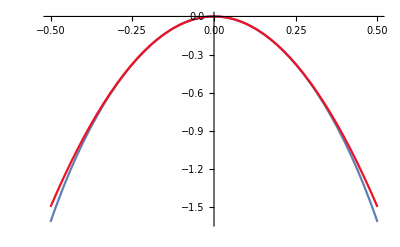

```mathematica
Show[Plot[(-(4 u^6)/((1-u^4)^(3/2))-(6 u^2)/(√(1-u^4))),{u,-0.5,0.5}],Plot[-6u^2,{u,-0.5,0.5},ColorFunction->Hue]]
```

```mathematica
D[Phi34[u],u]
```

ξ1+(u ξ2)/(2 (1-u^2)^(3/4))

```mathematica
Manipulate[Show[Plot[-ξ1^(1/4),{u,-1,1},PlotRange->All],Plot[ξ1^(1/4),{u,-1,1},PlotRange->All],Plot[-(2 u^3 ξ1)/(√(1-u^4))+ξ2,{u,-a,a},PlotRange->Full],Plot[ξ1+(u ξ2)/(2 (1-u^2)^(3/4)),{u,-(1-a^2)^(1/4),(1-a^2)^(1/4)},ColorFunction->Hue]],{ξ1,0,20},{ξ2,0,20},{a,0.001,0.999}]
```

```mathematica
Manipulate[Show[Plot[ξ1+(u ξ2)/(2 (1-u^2)^(3/4)),{u,-1,1}],Plot[ξ1+(u ξ2)/2,{u,-1,1},ColorFunction->Hue],Plot[-ξ1^(1/4),{u,-1,1}],Plot[ξ1^(1/4),{u,-1,1}]],{ξ1,0,100},{ξ2,0,ξ1^(1/4)}]
```

```mathematica
Manipulate[Plot[Sqrt[1-u^4]/(2*u^3) - (1-a^2)^(1/4)/(2*(1-Sqrt[1-a^2])^(3/4)),{u,-a,0}],{a,0.001,0.999}]
```

```mathematica
Manipulate[Plot[2*((1-u^2)^(3/4))/u  -  2*(Sqrt[1-b^4])^3/Sqrt[1-(1-b^4)^2],{u,0,b}],{b,0.001,0.999}]
```

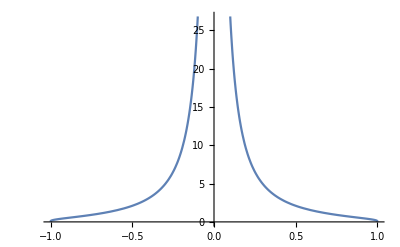

```mathematica
Plot[(1-a^2)^(1/4)/(2*(1-Sqrt[1-a^2])^(3/4)),{a,-1,1}]
```

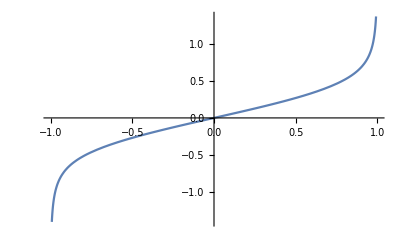

```mathematica
Plot[x/(2*(1-x^2)^(1/4)),{x,-1,1}]
```

```mathematica
N[3^(1/4)]
```

1.31607

```mathematica
Solve[α-ξ2==-2*u^3*ξ1,u]
```

{{u→-((-1/2)^(1/3) (-α+ξ2)^(1/3))/ξ1^(1/3)},{u→(-α+ξ2)^(1/3)/(2^(1/3) ξ1^(1/3))},{u→((-1)^(2/3) (-α+ξ2)^(1/3))/(2^(1/3) ξ1^(1/3))}}

```mathematica
-((-1/2)^(1/3) (α+ξ2)^(1/3))/ξ1^(1/3)+-((-1/2)^(1/3) (-α+ξ2)^(1/3))/ξ1^(1/3)
```

-((-1/2)^(1/3) (-α+ξ2)^(1/3))/ξ1^(1/3)-((-1/2)^(1/3) (α+ξ2)^(1/3))/ξ1^(1/3)

```mathematica
Solve[ξ1+(u ξ2)/2==β,u]
```

{{u→(2 (β-ξ1))/ξ2}}

```mathematica
D[8/(β+ξ2) + (β/ξ1)^(1/3),β]
```

1/(3 (β/ξ1)^(2/3) ξ1)-8/(β+ξ2)^2

```mathematica
Solve[1/(3 (β/ξ1)^(2/3) ξ1)-8/(β+ξ2)^2==0,β]
```

{{β→Root[ξ2^6+6 ξ2^5 #1+(-13824 ξ1+15 ξ2^4) #1^2+20 ξ2^3 #1^3+15 ξ2^2 #1^4+6 ξ2 #1^5+#1^6&,1]},{β→Root[ξ2^6+6 ξ2^5 #1+(-13824 ξ1+15 ξ2^4) #1^2+20 ξ2^3 #1^3+15 ξ2^2 #1^4+6 ξ2 #1^5+#1^6&,2]},{β→Root[ξ2^6+6 ξ2^5 #1+(-13824 ξ1+15 ξ2^4) #1^2+20 ξ2^3 #1^3+15 ξ2^2 #1^4+6 ξ2 #1^5+#1^6&,3]},{β→Root[ξ2^6+6 ξ2^5 #1+(-13824 ξ1+15 ξ2^4) #1^2+20 ξ2^3 #1^3+15 ξ2^2 #1^4+6 ξ2 #1^5+#1^6&,4]},{β→Root[ξ2^6+6 ξ2^5 #1+(-13824 ξ1+15 ξ2^4) #1^2+20 ξ2^3 #1^3+15 ξ2^2 #1^4+6 ξ2 #1^5+#1^6&,5]},{β→Root[ξ2^6+6 ξ2^5 #1+(-13824 ξ1+15 ξ2^4) #1^2+20 ξ2^3 #1^3+15 ξ2^2 #1^4+6 ξ2 #1^5+#1^6&,6]}}

```mathematica
D[Sqrt[1-u^4]/(2*u^3) - (1-a^2)^(1/4)/(2*(1-Sqrt[1-a^2])^(3/4)),u]
```

-1/(√(1-u^4))-(3 √(1-u^4))/(2 u^4)

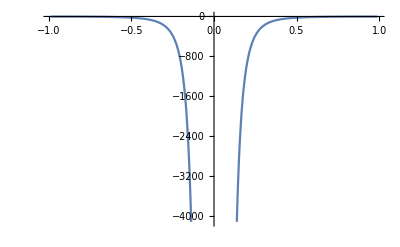

```mathematica
Plot[-1/(√(1-u^4))-(3 √(1-u^4))/(2 u^4),{u,-0.99,0.99}]
```

```mathematica
Series[Sqrt[1-a^4]/(2*a^3) - (1-a^2)^(1/4)/(2*(1-Sqrt[1-a^2])^(3/4)),{a,0,5}]
```

1/(2 a^3)-1/(2^(1/4) a^(3/2))+(7 √a)/(16 2^(1/4))-a/4+(51 a^(5/2))/(512 2^(1/4))+(417 a^(9/2))/(8192 2^(1/4))-a^5/16+O[a]^(11/2)

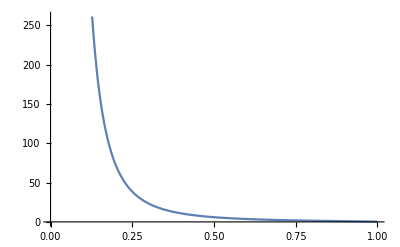

```mathematica
Plot[Sqrt[1-a^4]/(2*a^3) + (1-a^2)^(1/4)/(2*(1-Sqrt[1-a^2])^(3/4)),{a,0,1}]
```

```mathematica
Limit[Sqrt[1-a^4]/(2*a^3) + (1-a^2)^(1/4)/(2*(1-Sqrt[1-a^2])^(3/4)),a-> 1]
```

0

```mathematica
Series[(α+ξ2)^(1/3)-(ξ2-α)^(1/3),{,},{α,}]
```

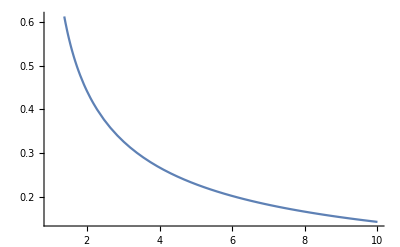

```mathematica
Plot[(1+δ)^(1/3)-(-1+δ)^(1/3),{δ,1,10}]
```

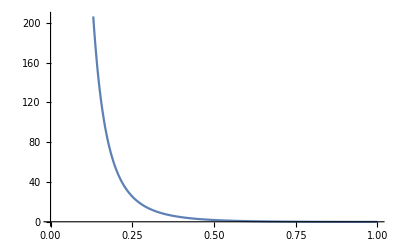

```mathematica
Plot[Sqrt[1-a^4]/(2a^3) - (1-a^2)^(1/4)/(2(1-Sqrt[1-a^2])^(3/4)),{a,0,1}]
```

```mathematica
Integrate[1/r^(5/4+1/8),{r,k1,k2}]
```

ConditionalExpression[8/3 (1/k1^(3/8)-1/k2^(3/8)),Re[k1]≥0&&Re[k2]≥0&&((Re[k1/(-k1+k2)]≥0&&k1^2≠k1 k2)||k1/(k1-k2)∉Reals||Re[k1/(k1-k2)]>1)]